## Build Transition Network

### CA30 Network

```mathematica
CAT=Association[Table[#->CellularAutomaton[30,#,{{{1}}}]&[IntegerDigits[i,2,3]],{i,0,7}]]
```

<|{0,0,0}→{0,0,0},{0,0,1}→{1,1,1},{0,1,0}→{1,1,1},{0,1,1}→{0,1,0},{1,0,0}→{1,1,1},{1,0,1}→{0,0,1},{1,1,0}→{1,0,0},{1,1,1}→{0,0,0}|>

### Other Networks

```mathematica
CAT=Association[{1->2,2->3,3->5,4->5,5->3,6->5}]
```

<|1→2,2→3,3→5,4→5,5→3,6→5|>

## Plot Graph

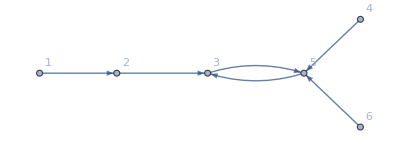

```mathematica
g=Graph[Normal@CAT,VertexLabels->"Name"]
```

## Main Function: Finding ϕ for T

```mathematica
AssociationSort[]
```

```mathematica
ForwardEvolution[$ϕ_,$Vp_,{$vi_,$vj_},$T_]:=Module[{ϕ=$ϕ,Vp=$Vp,vi=$vi,vj=$vj,T=$T},
While[¬KeyExistsQ[ϕ,T[vi]],
ϕ[T[vi]]=T[ϕ[vi]];
vi=T[vi];
vj=T[vj];
Vp=Complement[Vp,{vi}];
];
{ϕ,Vp,vi,vj,T}
]
```

```mathematica
Function
```

```mathematica
observed={};
```

```mathematica
Findϕ[ϕin_,Va_,Vall_,T_,d_]:=Module[{ϕ=ϕin,Vp=Va,vi,vj},
If[Va=={},Sow[KeySort[ϕ]];Return[],

Do[vi=Va⟦i⟧;vj=Vall⟦j⟧;
Vp=Va;ϕ=ϕin;(*Initialize*)
ϕ[vi]=vj;
Vp=Complement[Vp,{vi}];
If[¬MemberQ[observed,KeySort[ϕ]],

(*{ϕ,Vp,vi,vj,T}=ForwardEvolution[ϕ,Vp,{vi,vj},T];*)

(*Forward Evolution*)
While[¬KeyExistsQ[ϕ,T[vi]],
ϕ[T[vi]]=T[ϕ[vi]];
vi=T[vi];
vj=T[vj];
Vp=Complement[Vp,{vi}];
];

If[¬MemberQ[observed,KeySort[ϕ]],AppendTo[observed,KeySort[ϕ]]];

If[ϕ[T[vi]]==T[ϕ[vi]],
Vp=Complement[Vp,{T[vi]}];
Findϕ[ϕ,Vp,Vall,T,d+1](*,
Return[]*)];
]
,{i,1,Length[Va]},{j,1,Length[Vall]}];
]
]
```

## Experiments

```mathematica
observed={};
{ans,list}=Reap[Findϕ[<||>,Keys[CAT],Keys[CAT],CAT,1]];
```

```mathematica
observed={};
```

```mathematica
Length[list⟦1⟧]
```

88

```mathematica
Length[observed]
```

920

```mathematica
Length[Tally[observed,KeySort[#1]==KeySort[#2]&]]
```

920

```mathematica
list={DeleteDuplicates[list⟦1⟧]};
```

```mathematica
Length[list⟦1⟧]
```

44

```mathematica
DeleteDuplicates[list]
```

{{<|{0,0,0}→{0,0,0},{0,0,1}→{0,0,1},{1,1,1}→{1,1,1},{0,1,0}→{0,1,0},{0,1,1}→{0,1,1},{1,0,0}→{1,0,0},{1,0,1}→{1,0,1},{1,1,0}→{1,1,0}|>}}

```mathematica
groups=Tally[Sort[Sort/@WeaklyConnectedComponents[#]]&/@(Graph[Normal@#]&/@(Tally[list⟦1⟧]ᵀ⟦1⟧))];
```

```mathematica
syms=DeleteDuplicates[Graph[Normal@#]&/@(list⟦1⟧),IsomorphicGraphQ[#1,#2]&];
```

```mathematica
syms2=DeleteDuplicates[syms,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

```mathematica
Length[syms]
```

19

```mathematica
Length[syms2]
```

10

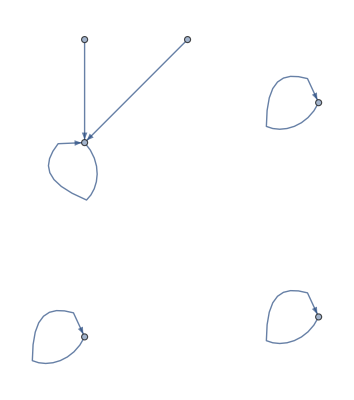
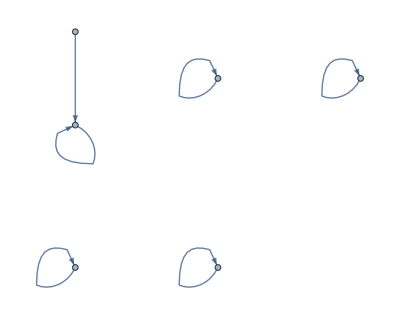
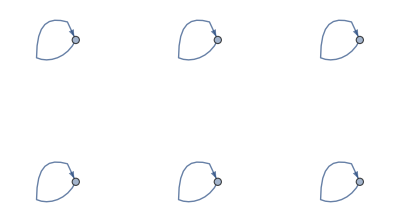
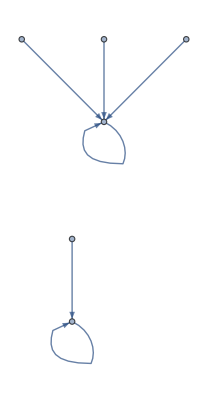
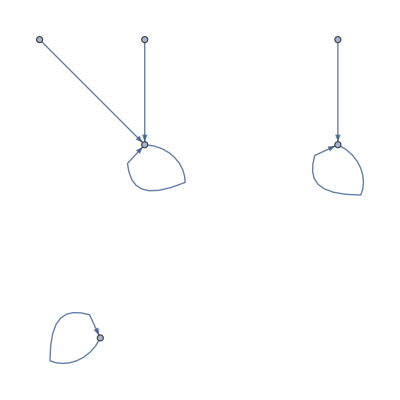
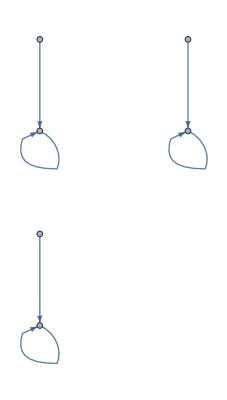
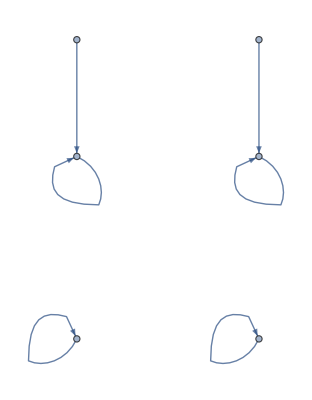
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
syms2
```

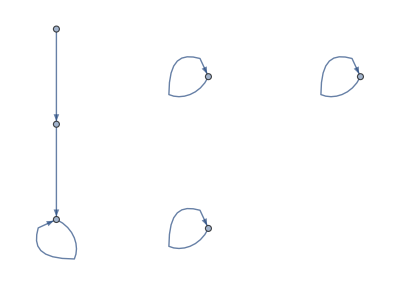
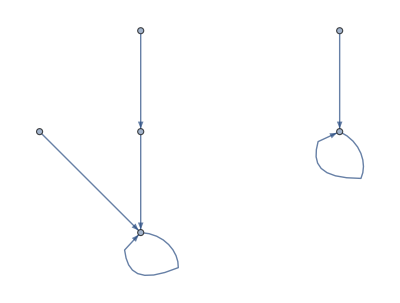
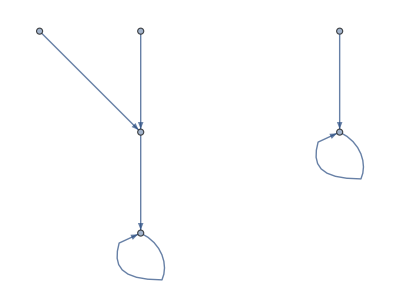
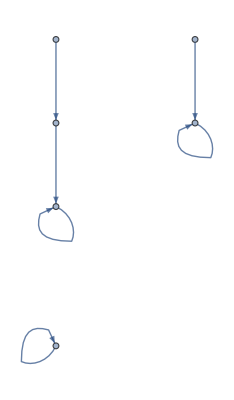
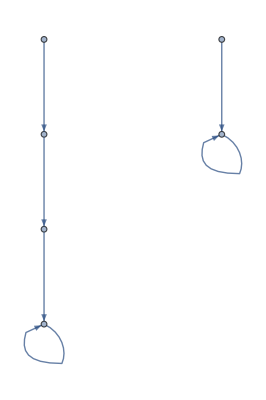
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
syms
```

```mathematica
LabelName=Table[IntegerDigits[i,2,3]->i,{i,0,7}];
```

```mathematica
LabelName=Thread[{1,2,3,4,5,6}->{1,2,3,4,5,6}]
```

{1→1,2→2,3→3,4→4,5→5,6→6}

```mathematica
CommunityGraphPlot[g,WeaklyConnectedComponents[syms2⟦2⟧],Method->"Hierarchical",VertexLabels->LabelName]
```

-Graphics-

```mathematica
Multicolumn[CommunityGraphPlot[g,WeaklyConnectedComponents[#],Method->"Hierarchical",VertexLabels->LabelName]&/@syms2,3]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
PropertyValue[{g,#},VertexCoordinates]&/@VertexList[g]
```

{{0.,0.},{-1.,2.},{0.,1.},{0.,2.},{0.,3.},{1.,2.},{-1.,3.},{1.,3.}}

```mathematica
Head[g]
```

Graph

```mathematica
Clear[CombineGraphs]
```

```mathematica
CombineGraphs[g,"1234"]
```

1234

```mathematica
CombineGraphs[g1_,g2_]:=HighlightGraph[Graph[Join[EdgeRules[g1],EdgeRules[g2]],VertexCoordinates->(PropertyValue[{g1,#},VertexCoordinates]&/@VertexList[g1])],EdgeRules[g2],GraphHighlightStyle->"Dashed"]

CombineGraphs[g1_,g2_,"Adaptive"]:=HighlightGraph[Graph[Join[EdgeRules[g1],EdgeRules[g2]]],EdgeRules[g2],GraphHighlightStyle->"Dashed"]
```

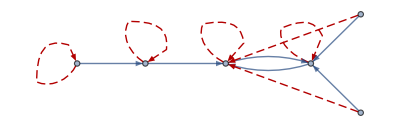
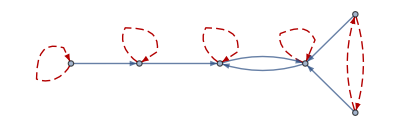
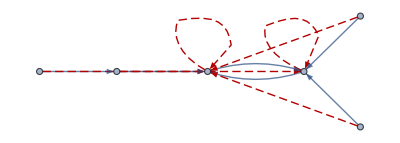
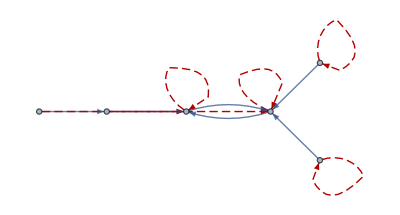
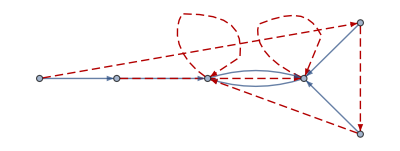
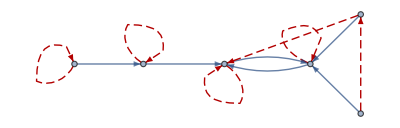
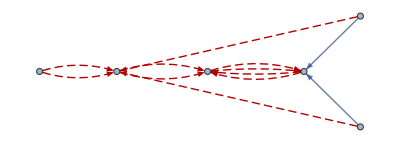
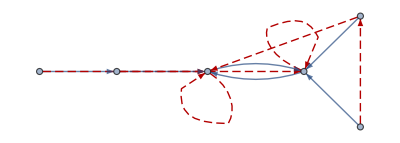
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
ϕplots=Multicolumn[CombineGraphs[g,#]&/@syms,5]
```

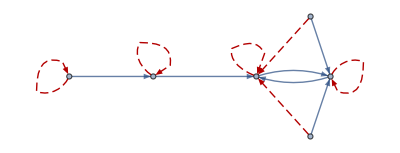
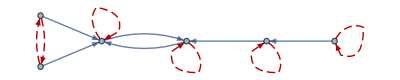
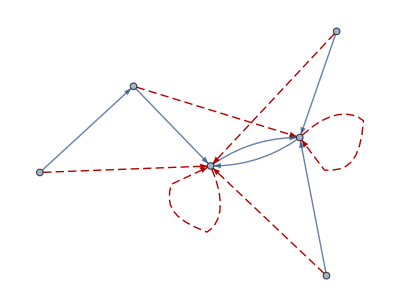
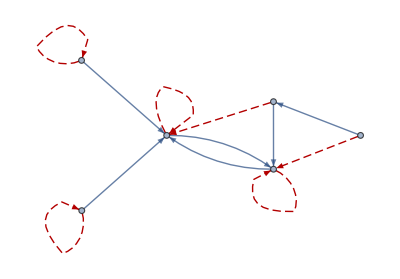
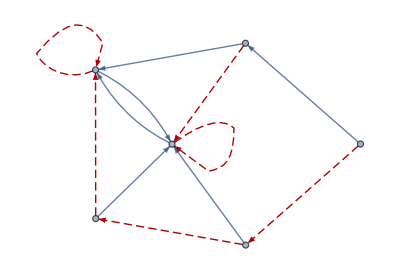
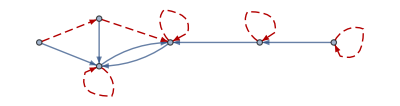
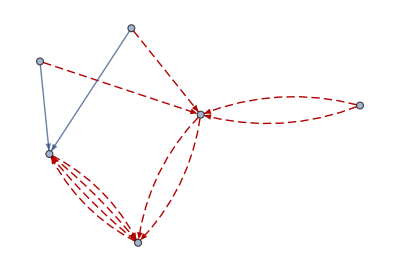
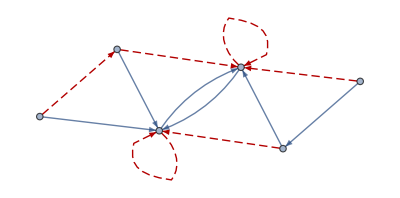
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
ϕplots=Multicolumn[CombineGraphs[g,#,"Adaptive"]&/@syms,5]
```

## Plots

```mathematica
{1,2,3,4}⟦1;;7⟧
```

Part::take: 无法在 {1,2,3,4} 中提取位置 1 至 7.

{1,2,3,4}⟦1;;7⟧

```mathematica
Take
```

```mathematica
symclasses=Gather[syms,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

```mathematica
symclassPlot1=Module[{tb=CombineGraphs[g,#]&/@Take[#,Min[Length[#],4]]&/@symclasses},
(*tb⟦1⟧=tb⟦1,1;;4⟧;
tb⟦1,4⟧="...";*)
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses,None},TableAlignments->Center]
]
```

-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  |

```mathematica
symclassPlot2=Module[{tb=CombineGraphs[g,#,"Adaptive"]&/@Take[#,Min[Length[#],4]]&/@symclasses},
(*tb⟦1⟧=tb⟦1,1;;4⟧;
tb⟦1,4⟧="...";*)
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses,None},TableAlignments->Center]
]
```

-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- |  |  | 
-Graphics- | -Graphics- |  |  |

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainPlot1.pdf"}],symclassPlot1]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainPlot1.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainPlot2.pdf"}],symclassPlot2]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainPlot2.pdf

## Every Component is loop:

```mathematica
symclasses=Gather[syms,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

Test if graph is made by Hamiltonian Graphs:

```mathematica
CyclingGraphQ[graph_]:=AllTrue[HamiltonianGraphQ/@(Subgraph[graph,#]&/@WeaklyConnectedComponents[graph]),#&]
```

```mathematica
Select[syms,CyclingGraphQ[#]&]
```

{-Graphics-,-Graphics-}

```mathematica
symsH=Select[syms,CyclingGraphQ[#]&];
symclasses2=Gather[symsH,Sort[Sort/@WeaklyConnectedComponents[#1]]==Sort[Sort/@WeaklyConnectedComponents[#2]]&];
```

```mathematica
symclassHPlot1=Module[{tb=CombineGraphs[g,#]&/@Take[#,Min[Length[#],4]]&/@symclasses2},
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses2,None},TableAlignments->Center]
]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
symclassHPlot2=Module[{tb=CombineGraphs[g,#,"Adaptive"]&/@Take[#,Min[Length[#],4]]&/@symclasses2},
TableForm[tb,TableHeadings->{CommunityGraphPlot[g,WeaklyConnectedComponents[#⟦1⟧],Method->"Hierarchical"]&/@symclasses2,None},TableAlignments->Center]
]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainHPlot1.pdf"}],symclassHPlot1]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainHPlot1.pdf

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"figures","CoarseGrainHPlot2.pdf"}],symclassHPlot2]
```

/Users/yanbozhang/项目 & 存档/01 科研项目/CausualEmergence/figures/CoarseGrainHPlot2.pdf